# *** BG METHOD FOR THE EVALUATION OF THE SPECTRAL DENSITY ***

## Inputs

### Input parameters

```mathematica
BarOmega = 0.5;
tmax = 30;
```

### Basis function, bins in t and in energy and plot of the basis function as a function of the energy

```mathematica
b[K_, t_] = E^(-t*K);
```

```mathematica
Binst = Table[Range[0, tmax, 1]];
```

```mathematica
BinsOm = Table[Range[0.0001, 27, 0.01]];
```

```mathematica
NBi= Dimensions[Binst];
NBins = NBi[[1]];
```

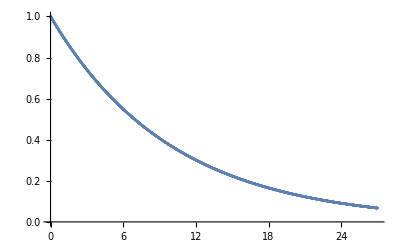

```mathematica
ListPlot[Transpose@{BinsOm, b[BinsOm, 0.1]}]
```

## Computation integrals for the evaluation of R,W

### Computation of R and Plot as a function of t

```mathematica
For[j=1, j<=NBins, j++, RMatrix[j] = Table[Integrate[b[K, j],{K, 0, Infinity}]]]
```

```mathematica
RPlot = Table[RMatrix[i], {i,1,NBins}];
```

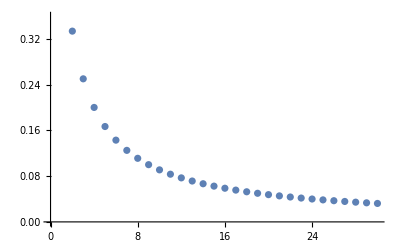

```mathematica
ListPlot[Transpose@{Binst, RPlot}]
```

```mathematica
Integrate[b[K,1]*b[K,1]*(K-1)^2, {K, 0, Infinity}]
```

1/4

### Computation of W and inversion

```mathematica
Clear[WMatrix]
```

```mathematica
For[j=1, j<=NBins, j++,For[i=1,i<=NBins,i++, WMatrix[i,j] = Table[Integrate[b[K,i]*b[K,j]*(K-BarOmega)^2,{K, 0, Infinity}]]; Print[WMatrix[i,j]]]]
```

0.125

0.0462963

0.03125

0.026

0.0231481

0.021137

0.0195313

0.0181756

0.017

0.0159654

0.0150463

0.0142239

0.013484

0.0128148

0.012207

0.0116528

0.0111454

0.0106794

0.01025

0.00985315

0.00948535

0.00914359

0.00882523

0.008528

0.00824989

0.00798913

0.00774417

0.00751363

0.0072963

0.00709107

0.00689697

0.0462963

0.03125

0.026

0.0231481

0.021137

0.0195313

0.0181756

0.017

0.0159654

0.0150463

0.0142239

0.013484

0.0128148

0.012207

0.0116528

0.0111454

0.0106794

0.01025

0.00985315

0.00948535

0.00914359

0.00882523

0.008528

0.00824989

0.00798913

0.00774417

0.00751363

0.0072963

0.00709107

0.00689697

0.00671314

0.03125

0.026

0.0231481

0.021137

0.0195313

0.0181756

0.017

0.0159654

0.0150463

0.0142239

0.013484

0.0128148

0.012207

0.0116528

0.0111454

0.0106794

0.01025

0.00985315

0.00948535

0.00914359

0.00882523

0.008528

0.00824989

0.00798913

0.00774417

0.00751363

0.0072963

0.00709107

0.00689697

0.00671314

0.00653877

0.026

0.0231481

0.021137

0.0195313

0.0181756

0.017

0.0159654

0.0150463

0.0142239

0.013484

0.0128148

0.012207

0.0116528

0.0111454

0.0106794

0.01025

0.00985315

0.00948535

0.00914359

0.00882523

0.008528

0.00824989

0.00798913

0.00774417

0.00751363

0.0072963

0.00709107

0.00689697

0.00671314

0.00653877

0.00637318

0.0231481

0.021137

0.0195313

0.0181756

0.017

0.0159654

0.0150463

0.0142239

0.013484

0.0128148

0.012207

0.0116528

0.0111454

0.0106794

0.01025

0.00985315

0.00948535

0.00914359

0.00882523

0.008528

0.00824989

0.00798913

0.00774417

0.00751363

0.0072963

0.00709107

0.00689697

0.00671314

0.00653877

0.00637318

0.00621571

0.021137

0.0195313

0.0181756

0.017

0.0159654

0.0150463

0.0142239

0.013484

0.0128148

0.012207

0.0116528

0.0111454

0.0106794

0.01025

0.00985315

0.00948535

0.00914359

0.00882523

0.008528

0.00824989

0.00798913

0.00774417

0.00751363

0.0072963

0.00709107

0.00689697

0.00671314

0.00653877

0.00637318

0.00621571

0.00606578

0.0195313

0.0181756

0.017

0.0159654

0.0150463

0.0142239

0.013484

0.0128148

0.012207

0.0116528

0.0111454

0.0106794

0.01025

0.00985315

0.00948535

0.00914359

0.00882523

0.008528

0.00824989

0.00798913

0.00774417

0.00751363

0.0072963

0.00709107

0.00689697

0.00671314

0.00653877

0.00637318

0.00621571

0.00606578

0.00592288

0.0181756

0.017

0.0159654

0.0150463

0.0142239

0.013484

0.0128148

0.012207

0.0116528

0.0111454

0.0106794

0.01025

0.00985315

0.00948535

0.00914359

0.00882523

0.008528

0.00824989

0.00798913

0.00774417

0.00751363

0.0072963

0.00709107

0.00689697

0.00671314

0.00653877

0.00637318

0.00621571

0.00606578

0.00592288

0.00578651

0.017

0.0159654

0.0150463

0.0142239

0.013484

0.0128148

0.012207

0.0116528

0.0111454

0.0106794

0.01025

0.00985315

0.00948535

0.00914359

0.00882523

0.008528

0.00824989

0.00798913

0.00774417

0.00751363

0.0072963

0.00709107

0.00689697

0.00671314

0.00653877

0.00637318

0.00621571

0.00606578

0.00592288

0.00578651

0.00565625

0.0159654

0.0150463

0.0142239

0.013484

0.0128148

0.012207

0.0116528

0.0111454

0.0106794

0.01025

0.00985315

0.00948535

0.00914359

0.00882523

0.008528

0.00824989

0.00798913

0.00774417

0.00751363

0.0072963

0.00709107

0.00689697

0.00671314

0.00653877

0.00637318

0.00621571

0.00606578

0.00592288

0.00578651

0.00565625

0.0055317

0.0150463

0.0142239

0.013484

0.0128148

0.012207

0.0116528

0.0111454

0.0106794

0.01025

0.00985315

0.00948535

0.00914359

0.00882523

0.008528

0.00824989

0.00798913

0.00774417

0.00751363

0.0072963

0.00709107

0.00689697

0.00671314

0.00653877

0.00637318

0.00621571

0.00606578

0.00592288

0.00578651

0.00565625

0.0055317

0.00541248

0.0142239

0.013484

0.0128148

0.012207

0.0116528

0.0111454

0.0106794

0.01025

0.00985315

0.00948535

0.00914359

0.00882523

0.008528

0.00824989

0.00798913

0.00774417

0.00751363

0.0072963

0.00709107

0.00689697

0.00671314

0.00653877

0.00637318

0.00621571

0.00606578

0.00592288

0.00578651

0.00565625

0.0055317

0.00541248

0.00529828

0.013484

0.0128148

0.012207

0.0116528

0.0111454

0.0106794

0.01025

0.00985315

0.00948535

0.00914359

0.00882523

0.008528

0.00824989

0.00798913

0.00774417

0.00751363

0.0072963

0.00709107

0.00689697

0.00671314

0.00653877

0.00637318

0.00621571

0.00606578

0.00592288

0.00578651

0.00565625

0.0055317

0.00541248

0.00529828

0.00518877

0.0128148

0.012207

0.0116528

0.0111454

0.0106794

0.01025

0.00985315

0.00948535

0.00914359

0.00882523

0.008528

0.00824989

0.00798913

0.00774417

0.00751363

0.0072963

0.00709107

0.00689697

0.00671314

0.00653877

0.00637318

0.00621571

0.00606578

0.00592288

0.00578651

0.00565625

0.0055317

0.00541248

0.00529828

0.00518877

0.00508368

0.012207

0.0116528

0.0111454

0.0106794

0.01025

0.00985315

0.00948535

0.00914359

0.00882523

0.008528

0.00824989

0.00798913

0.00774417

0.00751363

0.0072963

0.00709107

0.00689697

0.00671314

0.00653877

0.00637318

0.00621571

0.00606578

0.00592288

0.00578651

0.00565625

0.0055317

0.00541248

0.00529828

0.00518877

0.00508368

0.00498274

0.0116528

0.0111454

0.0106794

0.01025

0.00985315

0.00948535

0.00914359

0.00882523

0.008528

0.00824989

0.00798913

0.00774417

0.00751363

0.0072963

0.00709107

0.00689697

0.00671314

0.00653877

0.00637318

0.00621571

0.00606578

0.00592288

0.00578651

0.00565625

0.0055317

0.00541248

0.00529828

0.00518877

0.00508368

0.00498274

0.00488572

0.0111454

0.0106794

0.01025

0.00985315

0.00948535

0.00914359

0.00882523

0.008528

0.00824989

0.00798913

0.00774417

0.00751363

0.0072963

0.00709107

0.00689697

0.00671314

0.00653877

0.00637318

0.00621571

0.00606578

0.00592288

0.00578651

0.00565625

0.0055317

0.00541248

0.00529828

0.00518877

0.00508368

0.00498274

0.00488572

0.00479239

0.0106794

0.01025

0.00985315

0.00948535

0.00914359

0.00882523

0.008528

0.00824989

0.00798913

0.00774417

0.00751363

0.0072963

0.00709107

0.00689697

0.00671314

0.00653877

0.00637318

0.00621571

0.00606578

0.00592288

0.00578651

0.00565625

0.0055317

0.00541248

0.00529828

0.00518877

0.00508368

0.00498274

0.00488572

0.00479239

0.00470255

0.01025

0.00985315

0.00948535

0.00914359

0.00882523

0.008528

0.00824989

0.00798913

0.00774417

0.00751363

0.0072963

0.00709107

0.00689697

0.00671314

0.00653877

0.00637318

0.00621571

0.00606578

0.00592288

0.00578651

0.00565625

0.0055317

0.00541248

0.00529828

0.00518877

0.00508368

0.00498274

0.00488572

0.00479239

0.00470255

0.004616

0.00985315

0.00948535

0.00914359

0.00882523

0.008528

0.00824989

0.00798913

0.00774417

0.00751363

0.0072963

0.00709107

0.00689697

0.00671314

0.00653877

0.00637318

0.00621571

0.00606578

0.00592288

0.00578651

0.00565625

0.0055317

0.00541248

0.00529828

0.00518877

0.00508368

0.00498274

0.00488572

0.00479239

0.00470255

0.004616

0.00453257

0.00948535

0.00914359

0.00882523

0.008528

0.00824989

0.00798913

0.00774417

0.00751363

0.0072963

0.00709107

0.00689697

0.00671314

0.00653877

0.00637318

0.00621571

0.00606578

0.00592288

0.00578651

0.00565625

0.0055317

0.00541248

0.00529828

0.00518877

0.00508368

0.00498274

0.00488572

0.00479239

0.00470255

0.004616

0.00453257

0.00445209

0.00914359

0.00882523

0.008528

0.00824989

0.00798913

0.00774417

0.00751363

0.0072963

0.00709107

0.00689697

0.00671314

0.00653877

0.00637318

0.00621571

0.00606578

0.00592288

0.00578651

0.00565625

0.0055317

0.00541248

0.00529828

0.00518877

0.00508368

0.00498274

0.00488572

0.00479239

0.00470255

0.004616

0.00453257

0.00445209

0.00437442

0.00882523

0.008528

0.00824989

0.00798913

0.00774417

0.00751363

0.0072963

0.00709107

0.00689697

0.00671314

0.00653877

0.00637318

0.00621571

0.00606578

0.00592288

0.00578651

0.00565625

0.0055317

0.00541248

0.00529828

0.00518877

0.00508368

0.00498274

0.00488572

0.00479239

0.00470255

0.004616

0.00453257

0.00445209

0.00437442

0.0042994

0.008528

0.00824989

0.00798913

0.00774417

0.00751363

0.0072963

0.00709107

0.00689697

0.00671314

0.00653877

0.00637318

0.00621571

0.00606578

0.00592288

0.00578651

0.00565625

0.0055317

0.00541248

0.00529828

0.00518877

0.00508368

0.00498274

0.00488572

0.00479239

0.00470255

0.004616

0.00453257

0.00445209

0.00437442

0.0042994

0.0042269

0.00824989

0.00798913

0.00774417

0.00751363

0.0072963

0.00709107

0.00689697

0.00671314

0.00653877

0.00637318

0.00621571

0.00606578

0.00592288

0.00578651

0.00565625

0.0055317

0.00541248

0.00529828

0.00518877

0.00508368

0.00498274

0.00488572

0.00479239

0.00470255

0.004616

0.00453257

0.00445209

0.00437442

0.0042994

0.0042269

0.0041568

0.00798913

0.00774417

0.00751363

0.0072963

0.00709107

0.00689697

0.00671314

0.00653877

0.00637318

0.00621571

0.00606578

0.00592288

0.00578651

0.00565625

0.0055317

0.00541248

0.00529828

0.00518877

0.00508368

0.00498274

0.00488572

0.00479239

0.00470255

0.004616

0.00453257

0.00445209

0.00437442

0.0042994

0.0042269

0.0041568

0.00408898

0.00774417

0.00751363

0.0072963

0.00709107

0.00689697

0.00671314

0.00653877

0.00637318

0.00621571

0.00606578

0.00592288

0.00578651

0.00565625

0.0055317

0.00541248

0.00529828

0.00518877

0.00508368

0.00498274

0.00488572

0.00479239

0.00470255

0.004616

0.00453257

0.00445209

0.00437442

0.0042994

0.0042269

0.0041568

0.00408898

0.00402333

0.00751363

0.0072963

0.00709107

0.00689697

0.00671314

0.00653877

0.00637318

0.00621571

0.00606578

0.00592288

0.00578651

0.00565625

0.0055317

0.00541248

0.00529828

0.00518877

0.00508368

0.00498274

0.00488572

0.00479239

0.00470255

0.004616

0.00453257

0.00445209

0.00437442

0.0042994

0.0042269

0.0041568

0.00408898

0.00402333

0.00395975

0.0072963

0.00709107

0.00689697

0.00671314

0.00653877

0.00637318

0.00621571

0.00606578

0.00592288

0.00578651

0.00565625

0.0055317

0.00541248

0.00529828

0.00518877

0.00508368

0.00498274

0.00488572

0.00479239

0.00470255

0.004616

0.00453257

0.00445209

0.00437442

0.0042994

0.0042269

0.0041568

0.00408898

0.00402333

0.00395975

0.00389815

0.00709107

0.00689697

0.00671314

0.00653877

0.00637318

0.00621571

0.00606578

0.00592288

0.00578651

0.00565625

0.0055317

0.00541248

0.00529828

0.00518877

0.00508368

0.00498274

0.00488572

0.00479239

0.00470255

0.004616

0.00453257

0.00445209

0.00437442

0.0042994

0.0042269

0.0041568

0.00408898

0.00402333

0.00395975

0.00389815

0.00383843

0.00689697

0.00671314

0.00653877

0.00637318

0.00621571

0.00606578

0.00592288

0.00578651

0.00565625

0.0055317

0.00541248

0.00529828

0.00518877

0.00508368

0.00498274

0.00488572

0.00479239

0.00470255

0.004616

0.00453257

0.00445209

0.00437442

0.0042994

0.0042269

0.0041568

0.00408898

0.00402333

0.00395975

0.00389815

0.00383843

0.0037805

```mathematica
WM = Table[WMatrix[i,j],{i,1,NBins},{j,1,NBins}];
```

```mathematica
WMM1 = Inverse[Rationalize[WM]]
```

{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}
 |  |  |  |

## Computation of the coefficients g_t

```mathematica
For[j=1, j<=NBins, j++,NVector[j]=0]
```

```mathematica
For[j=1, j<=NBins, j++,For[i=1,i<=NBins,i++, NVector[j] = NVector[j] +RMatrix[i]*WMM1[[j,i]]]; Print[N[NVector[j],10]]]
```

-48.18768236

44778.07764

-9.799852774×10^6

9.862369683×10^8

-5.677648165×10^10

2.102191815×10^12

-5.388733174×10^13

1.005868348×10^15

-1.418108108×10^16

1.55206507×10^17

-1.346844347×10^18

9.421236859×10^18

-5.381965535×10^19

2.536766459×10^20

-9.945201714×10^20

3.262856136×10^21

-8.998266654×10^21

2.091927533×10^22

-4.105436018×10^22

6.800369935×10^22

-9.490596808×10^22

1.11191038×10^23

-1.087268654×10^23

8.797797048×10^22

-5.819296735×10^22

3.092237634×10^22

-1.287166374×10^22

4.04031183×10^21

-8.988406916×10^20

1.262708991×10^20

-8.419436693×10^18

```mathematica
DScal = 0
```

0

```mathematica
For[j=1, j<=NBins, j++,For[i=1,i<=NBins,i++, DScal = DScal +(RMatrix[j]*RMatrix[i])*WMM1[[j,i]]]]
```

```mathematica
Print[DScal]
```

159561320014696323572262474909614424558915120994944133910242966055785911782538273359435976665263291602192252454924706264888881915147259134090461482992603501623067745542136226284320416088642709849277381680853434606824155984814919040182779517910990977289323417726067058649380039234114729336435153448237201425518691391527148152609763073031489191916902074282919553971047393196265034911896795081487279161318734158792284799667785908852890629078451778478480387128055616512470691196866404866040867036594644391583495438953130274087257084238361082444817366493456524658533016417151164465289110131784582787100212366640538993213867174059479623491989838876736872212563142921286459738169010246593507701919859354488533900839636927820146971024020486340589874447093930213706041267296966146813443553218206381418494249951811211360031007213428815898201806524590465966707754085183121502121455004264154718164301250392595518370449712905457923499602473421572115547874082169182402611622908018012867660502286194090044515578917943862565900811699722811767622664520786592609441576828097845611249978809095320065635136403590803206327471234251101754285248/1284035334720569635462470816404369982820539034181576998850676822565299879872345465363305087438871817385683999099771535622424286160823720835317423311144459256996489598755579185801826932885684642389591731836688533213256031908641365273787322440095441861907543358064988202913294872849761049480772799544178675171023656087672591855117276937854344833095761518456729319819103295955274652976826810682910824598144127429643580452231968692791732143143157759459584380595822602290425824193971112290990350277704919267523652157451261772022715432284443036383639736031280436914445400615665408898351111207984062643048366800353220306602534831276150422260469446484490005396833575881111189469363109824741664466213515144256228967197869905613055066290506737399751682737927135657356189258622373217690712651132652879579699575375857181236940326793529855068940989234070046695790734619310671342332157358932298703406996110564902661370213592919525726605588938389060521879000549062976504474466476080199147497141261217132096606960768420563170577863641427679455062663220538416190229263373757298686245641143225786012410622107943913007265172464282316189371

```mathematica
For[j=1, j<=NBins, j++, qFin[j] = NVector[j]/DScal; Print[N[qFin[j],10]]]
```

-0.3877799886

360.3419294

-78862.20317

7.936529452×10^6

-4.568964998×10^8

1.691693558×10^10

-4.336466886×10^11

8.094508749×10^12

-1.141191938×10^14

1.248990916×10^15

-1.083843962×10^16

7.581537319×10^16

-4.331020774×10^17

2.041408136×10^18

-8.003186744×10^18

2.625713156×10^19

-7.241161162×10^19

1.683433598×10^20

-3.303761156×10^20

5.472451146×10^20

-7.637353243×10^20

8.947859145×10^20

-8.749560168×10^20

7.079837567×10^20

-4.682953632×10^20

2.488411593×10^20

-1.035819399×10^20

3.25135387×10^19

-7.23322675×10^18

1.016137847×10^18

-6.775360226×10^16

### Plot of g_t as a function of the bins of t

```mathematica
qPlot = Table[qFin[j], {j,1,NBins}]
```

```mathematica
Print[N[qPlot,10]]
```

{-0.3877799886,360.3419294,-78862.20317,7.936529452×10^6,-4.568964998×10^8,1.691693558×10^10,-4.336466886×10^11,8.094508749×10^12,-1.141191938×10^14,1.248990916×10^15,-1.083843962×10^16,7.581537319×10^16,-4.331020774×10^17,2.041408136×10^18,-8.003186744×10^18,2.625713156×10^19,-7.241161162×10^19,1.683433598×10^20,-3.303761156×10^20,5.472451146×10^20,-7.637353243×10^20,8.947859145×10^20,-8.749560168×10^20,7.079837567×10^20,-4.682953632×10^20,2.488411593×10^20,-1.035819399×10^20,3.25135387×10^19,-7.23322675×10^18,1.016137847×10^18,-6.775360226×10^16}

```mathematica
ListLinePlot[Transpose@{Binst, qPlot}, PlotRange->{{0,31},{-1*^21,+1*^21}}, PlotMarkers->{Automatic, 10}]
```

-Graphics-

## Computation of the smearing function Delta and plot

```mathematica
DeltaBar[Om_] = Sum[N[qFin[i],100]*b[Om,i],{i,NBins}]
```

-6.775360225969305118207970330803135135122518577972175846334611916609726050590397939282505262615305579×10^16 ⅇ^(-31 Om)+1.016137846665756691660161997692344946235186655723473162406192493019521493313842657420132120034328693×10^18 ⅇ^(-30 Om)-7.233226750443556837659715523706066662509769407266550023875305295783373114735597770373750679473299213×10^18 ⅇ^(-29 Om)+3.251353869887915002377473254056900843282907774120165235723189436005155922535572997325865615904682911×10^19 ⅇ^(-28 Om)-1.035819399223442897294178711891746302411468324040126259023158053440565077669359893580301797264745917×10^20 ⅇ^(-27 Om)+2.488411593063904534773740493449709267887716662012964657673196590319774803638556231215496629960108486×10^20 ⅇ^(-26 Om)-4.682953632425093804887388588998077330371417091028368274575625082107481342562224691133970748769622725×10^20 ⅇ^(-25 Om)+7.079837567494629356906382005833100360739273198507582068793446939463891851137377102829214205469728292×10^20 ⅇ^(-24 Om)-8.749560167870744366395802341287879709168425478944627545200293697534121455708747315278576128630925245×10^20 ⅇ^(-23 Om)+8.947859145094306391739224116922596153122341572091373777460142039400478648660202967725357470420870847×10^20 ⅇ^(-22 Om)-7.637353242884508152663832757744904489045428140376727051700851616903409404798740963879220480186657798×10^20 ⅇ^(-21 Om)+5.47245114595149743383427181059223287190960757013027409215984755380852715700451825769087644753629447×10^20 ⅇ^(-20 Om)-3.303761156335255977417790730887233411931845721312457027927680980124237024576147143266002367239997123×10^20 ⅇ^(-19 Om)+1.683433597876292482310839823869363518793240191832160922354239059851597904473338699592156125719832115×10^20 ⅇ^(-18 Om)-7.241161162138939113944764726783036753470170310114173947337753667576537355748534634115747861175168254×10^19 ⅇ^(-17 Om)+2.625713155653645112894861706607116813771400405042275413513955178632065265294811586230756731548720885×10^19 ⅇ^(-16 Om)-8.003186743752422714597978874519681331706705704671662038981109763440072166922486505674503935412625415×10^18 ⅇ^(-15 Om)+2.041408136351010247698459908868548704728869716332096026895927064202666915785503725242354975485371032×10^18 ⅇ^(-14 Om)-4.331020773759184834580975804544262572151765246381084788705837784566018815474435574279008601906334438×10^17 ⅇ^(-13 Om)+7.581537319325600063132944422122131559146872379869381886363063554204162485232253127762436582585339982×10^16 ⅇ^(-12 Om)-1.083843961513684667298560883950100562660462958075365418638816898106236668921676304923267168375728493×10^16 ⅇ^(-11 Om)+1.248990915794500817538451026673621098644581468888533629763003428289027671435181755421945459683300067×10^15 ⅇ^(-10 Om)-1.141191937568779838947691463852330032795331135419599403948093968285968434053035043256243443344112994×10^14 ⅇ^(-9 Om)+8.094508748725766315910323737420555075210616011599451807762522532223301223359909202719124961857890662×10^12 ⅇ^(-8 Om)-4.336466885616943057731393561143011242246654676090800448074214497683421553230601018555610156903719452×10^11 ⅇ^(-7 Om)+1.691693557538069315943463105453249097080461941808784107177293289487701686221354290091577792190713839×10^10 ⅇ^(-6 Om)-4.568964997818986225236124143973950892782850832015025853280072408050322410849830144655988699375844569×10^8 ⅇ^(-5 Om)+7.936529451712703574493397552376782788122883840257136989551314197437300108398920362845181693782589316×10^6 ⅇ^(-4 Om)-78862.20316659355770330043509103871285897683104287968066278118136271725635817041605837177552247263598 ⅇ^(-3 Om)+360.3419293880567982560883763920953438607671955490119819438694400678332399803901974680659814344273815 ⅇ^(-2 Om)-0.3877799885789069981979404372842065238634583874677303225981290457306751201155895167644501349797427734 ⅇ^-Om

```mathematica
N[DeltaBar[0.5],10]
```

7.5

### Plot of Delta as a function of the Energy

```mathematica
Binnaggio = Range[0.0, 1, 0.01];
```

```mathematica
Dimensions[Binnaggio]
```

{101}

```mathematica
AAA =Table[DeltaBar[Binnaggio]];
```

```mathematica
BBB = Table[Binnaggio];
```

```mathematica
sdata = Transpose@{BBB, AAA};
```

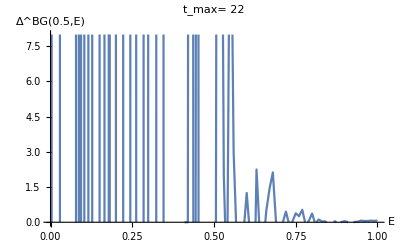

```mathematica
AAA =ListLinePlot[sdata, PlotRange->{{0,1},{0,8}}, AxesLabel->{"E","Δ^BG(0.5,E)"}, PlotLabel->"t_max= 22"]
```

### Output

```mathematica
Export["/Users/manuel/Documents/GitHub/Conducibility/Programmi/Delta_3.10.png",AAA]
```

/Users/manuel/Documents/GitHub/Conducibility/Programmi/Delta_3.10.png